```mathematica
Exit[]
```

### 2.2 (Holmes)

```mathematica
f= x^3+ ϵ x - 8;
p=f/.x-> 2 + a1 ϵ + a2 ϵ^2+a3 ϵ^3+O[ϵ]^4;
```

```mathematica
plist=CoefficientList[p,ϵ]
```

{0,2+12 a1,a1+8 ((3 a1^2)/4+(3 a2)/2),a2+8 (a1 a2+1/2 a1 (a1^2/4+a2)+(3 a3)/2)}

```mathematica
plist[[2]]
```

2+12 a1

```mathematica
Solve[Coefficient[p,ϵ,1]==0,a1]
```

{{a1→-1/6}}

```mathematica
Coefficient[p,ϵ,2]
```

a1+8 ((3 a1^2)/4+(3 a2)/2)

```mathematica
Solve[(Coefficient[p,ϵ,2]/.a1->-1/6)==0,a2]
```

{{a2→0}}

```mathematica
Solve[(Coefficient[p,ϵ,3]/.a1->-1/6/.a2->0)==0,a3]
```

{{a3→1/2592}}

#### Checking the approximation

```mathematica
root[ϵ_]:= x/.First@NSolve[x^3+ ϵ x - 8==0,x,Reals,WorkingPrecision->100];
approx[ϵ_]:= 2-1/6 ϵ + 1/2592 ϵ^3;
approxlow[ϵ_]:= 2-1/6 ϵ ;
approxwrong[ϵ_]:= 2-1/6 ϵ+ 1/2582 ϵ^3;
```

```mathematica
root[0.1]
```

1.98333

```mathematica
root[0.1`20]
```

1.98333372235052225764253440796415613718626482744257362092998865773003965281968651483608703162329065

```mathematica
approx[0.1`20]
```

1.983333719135802469136

```mathematica
approxwrong[0.1`20]
```

1.983333720630002581978

```mathematica
Table[root[1/10^n]-approx[1/10^n],{n,1,10}]//TableForm
```

3.214719788506731938828353668050658260275501219525636040724729853591726292227220467505679877×10^-9
3.21501759615987991454424368374451377493005443958410053067497574104852190694016083309748×10^-13
3.2150205463598772973873568593267891799608488672517570553513333843398317476566232953×10^-17
3.215020575833997051508599159310874300989327538964202030647084017234100131415912×10^-21
3.21502057612871036879362108164774304855490664506161962871830561103772310082×10^-25
3.2150205761316574740862147459101763311112895584940611678096383263914351×10^-29
3.215020576131686945111260425994195498654028991230458565753039586368×10^-33
3.21502057613168723982148300253847704872224762853865483699014687×10^-37
3.2150205761316872427685852004236633055809581872682378328218×10^-41
3.215020576131687242798056222374634911590903317583701672×10^-45

```mathematica
Table[Log[Abs[root[1/10^n]-approx[1/10^n]]]/Log[1/10^n],{n,1,10}]//TableForm
```

8.4928568764283714209123928589620294032918277600217840138395380444185166857631271991819185788
6.24640832289488330050528187595092997583062179922360931129036171290234780033978746852604
5.49760541575594821803453389226680407152121423405213994200012392533844235246351981813
5.1232040608215983559702402386759504805327960934354082189174594638455909310065523
4.898563248649316535582094492574161084997136737015203242450139902210289491784
4.748802707207697429036155577826927249303253672080355505689185549120629006
4.6418308918923115133119663180436587359353192153114730655073995532088
4.5616020304057725691716795375058370214370705867930024377508311988
4.499201804805131172552814780505583833375520437573965748125399
4.44928162432461805529713519917990562311306127789566046058

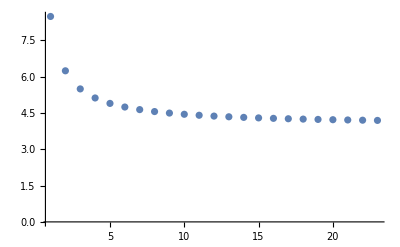

```mathematica
ListPlot[Table[Log[Abs[root[1/10^n]-approx[1/10^n]]]/Log[1/10^n],{n,1,100}],PlotRange->All]
```

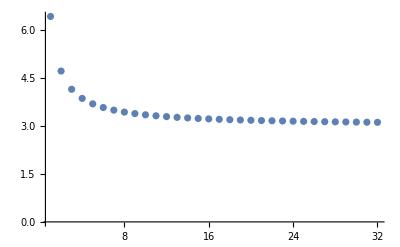

```mathematica
ListPlot[Table[Log[Abs[root[1/10^n]-approxwrong[1/10^n]]]/Log[1/10^n],{n,1,100}],PlotRange->All]
```

```mathematica
err[p_]:= root[1/10^p]-approx[1/10^p];
```

```mathematica
Table[-Log[err[p+1]/err[p]]/Log[10],{p,1,10}]//TableForm
```

3.999959769361395180098170892939830548369415838425434608741185381386178914916447737870162
3.99999960147807805309303792489855226290239910370920120341964835021063145671098451733
3.9999999960185487697773592779033897075675416715852130496694660793670366666356497
3.999999999960189254029511508167003502854499311334383336580861655669083734892
3.99999999999960189630646100409075807083383834740611682188441378367232658
3.9999999999999960189668307593440476557277124746981784244166835777378
3.999999999999999960189672073741085019949330187163708043454852718
3.99999999999999999960189672450355832888311924382167223112194
3.9999999999999999999960189672488017307509288407909128726
3.999999999999999999999960189672491783454969727458493

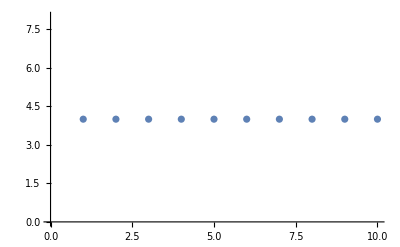

```mathematica
ListPlot[Table[-Log[err[p+1]/err[p]]/Log[10],{p,1,10}]]
```

```mathematica
err2[p_]:= root[1/10^p]-approxlow[1/10^p];
Table[-Log[err2[p+1]/err2[p]]/Log[10],{p,1,10}]//TableForm
```

3.003242027452873667663188794630846952379003486709297515209325092497394477263704385165526478
3.000325571321500719542934034191362650496822869807332181690118413507343885552736201032087
3.000032570593004373632123304499484749393144616864472828134089452572961311480033577695
3.000003257193685150495564150572235492501197491244586703476609026818186587893207203
3.000000325720712138459639876019678708325710824660111687794581292657295543895176
3.000000032572084649856354454896944948355259984147682381347609626300336445501
3.000000003257208599345515640882686744439217733355421087293105305196544352
3.00000000032572086127815014233302737595989975205112625529237964222699
3.000000000032572086141250999792041164263832091947341631088644399663
3.000000000003257208614259459834567791533801679021547048200595277

```mathematica
err3[p_]:= root[1/10^p]-approxwrong[1/10^p];
Table[-Log[Abs[err3[p+1]/err3[p]]]/Log[10],{p,1,10}]//TableForm
```

3.166473328237250589735180975665056183537662070389621280288373753057403404698674482778299
2.904224117682193462578491497878506661010736519936781348525801253976508953124139185903
2.991488896461002903227083456372039597731358744185722797127481788048065314416085051
2.999157992026169596074082429455478092424570366177216093655398255607862458677288
2.999915888919471186317784716397422790194340711996624504330812221050172473321
2.999991589787829828266454117698229147521142515615932820960728376150567678
2.999999158987740526165370961481494417232614580610936175836555605743218
2.999999915898863626766373874364303641379914828058059290817553881874
2.999999991589887258416852225452137963712123775409430091543235922
2.999999999158988734799086087397675465477348237034178144792043

### Problem 2.2 (Holmes)

```mathematica
Manipulate[Plot[Sin[ϵ x],{x,-π/ϵ,π/ϵ}],{ϵ,0.001`10,0.1`10}]
```

```mathematica
f=Sin[ϵ x] +2x-1;
f/.x->  1/2+a1 ϵ + a2 ϵ^2+a3 ϵ^3+a4 ϵ^4 +O[ϵ]^5
```

(1/2+2 a1) ϵ+(a1+2 a2) ϵ^2+(-1/48+a2+2 a3) ϵ^3+(-a1/8+a3+2 a4) ϵ^4+O[ϵ]^5

```mathematica
Solve[-1/48+a2+2 a3==0,a3]/.a1-> -1/4/.a2-> 1/8
```

{{a3→-5/96}}

### Problem 2.12 (Holmes)

```mathematica
Exit[]
```

```mathematica
eqn=D[u[t],t]+1+u[t]-ϵ u[t]^2;
```

```mathematica
eqn/.ϵ->0
```

1+u[t]+u'[t]

```mathematica
DSolve[{(eqn/.ϵ->0)==0, u[0]==0},u,t]
```

{{u→Function[{t},-ⅇ^-t (-1+ⅇ^t)]}}

```mathematica
Expand[-ⅇ^-t (-1+ⅇ^t)]
```

-1+ⅇ^-t

```mathematica
eqn/.ϵ->0/.u-> Function[{t},Exp[-t]-1]
```

0

```mathematica
eqn/.u->Function[{t},u0[t]+ϵ u1[t] + ϵ^2 u2[t] + O[ϵ]^3]
```

(1+u0[t]+u0'[t])+(-u0[t]^2+u1[t]+u1'[t]) ϵ+(-2 u0[t] u1[t]+u2[t]+u2'[t]) ϵ^2+O[ϵ]^3

```mathematica
p=eqn/.u->Function[{t},-Exp[-t] (-1+Exp[t])+ϵ u1[t] + ϵ^2 u2[t] + O[ϵ]^3]
```

(-(-1+ⅇ^-t)^2+u1[t]+u1'[t]) ϵ+(-2 (-1+ⅇ^-t) u1[t]+u2[t]+u2'[t]) ϵ^2+O[ϵ]^3

```mathematica
plist
```

{0,-(-1+ⅇ^-t)^2+u1[t]+u1'[t],-2 (-1+ⅇ^-t) u1[t]+u2[t]+u2'[t]}

```mathematica
plist=CoefficientList[p,ϵ];
```

```mathematica
DSolve[{plist[[2]]==0,u1[0]==0},u1,t]
```

{{u1→Function[{t},ⅇ^(-2 t) (-1+ⅇ^(2 t)-2 ⅇ^t t)]}}

```mathematica
Expand[ⅇ^(-2 t) (-1+ⅇ^(2 t)-2 ⅇ^t t)]
```

1-ⅇ^(-2 t)-2 ⅇ^-t t

```mathematica
plist[[2]]
```

-(-1+ⅇ^-t)^2+u1[t]+u1'[t]

```mathematica
plist[[2]]/.u1-> Function[{t},1-Exp[-2t]-2t Exp[-t]]//Simplify
```

0

```mathematica
plist[[3]]/.u1-> Function[{t},1-Exp[-2t]-2t Exp[-t]]
```

-2 (-1+ⅇ^-t) (1-ⅇ^(-2 t)-2 ⅇ^-t t)+u2[t]+u2'[t]

```mathematica
DSolve[{(plist[[3]]/.u1-> Function[{t},1-Exp[-2t]-2t Exp[-t]])==0,u2[0]==0},u2,t]//Simplify[#,Assumptions->t>0]&
```

{{u2→Function[{t},-ⅇ^(-3 t) (-1-2 ⅇ^t+ⅇ^(2 t)+2 ⅇ^(3 t)-4 ⅇ^t t-2 ⅇ^(2 t) t-2 ⅇ^(2 t) t^2)]}}

```mathematica
-ⅇ^(-3 t) (-1-2 ⅇ^t+ⅇ^(2 t)+2 ⅇ^(3 t)-4 ⅇ^t t-2 ⅇ^(2 t) t-2 ⅇ^(2 t) t^2)//Expand
```

-2+ⅇ^(-3 t)+2 ⅇ^(-2 t)-ⅇ^-t+4 ⅇ^(-2 t) t+2 ⅇ^-t t+2 ⅇ^-t t^2

```mathematica
4 ⅇ^(-2 t) t+2 ⅇ^-t t//Simplify
```

2 ⅇ^(-2 t) (2+ⅇ^t) t

#### Testing the approximation

```mathematica
approx[ϵ_]:= -1+ⅇ^-t + ϵ (1-ⅇ^(-2 t)-2 ⅇ^-t t) + ϵ^2(-2+ⅇ^(-3 t)+2 ⅇ^(-2 t)-ⅇ^-t+4 ⅇ^(-2 t) t+2 ⅇ^-t t+2 ⅇ^-t t^2);
```

```mathematica
full[ϵ_]:=u[t]/.First@NDSolve[{D[u[t],t]+1+u[t]-ϵ u[t]^2==0,u[0]==0},u,{t,0,10},WorkingPrecision->50];
```

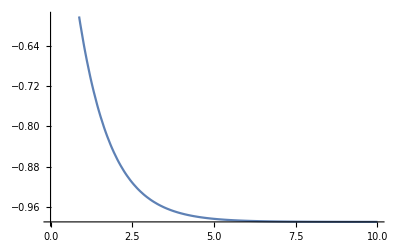

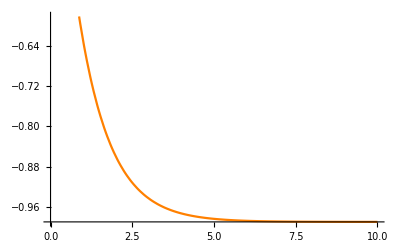

```mathematica
p1=Plot[approx[1/100],{t,0,10}]
p2=Plot[Evaluate[full[1/100]],{t,0,10},PlotStyle->Orange]
```

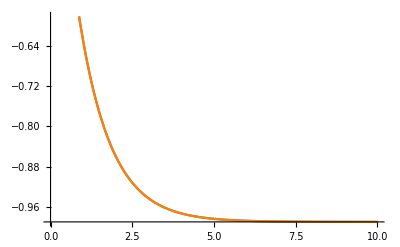

```mathematica
Show[p1,p2]
```

```mathematica
err[t_]=Log[ Abs[(approx[1/100]-full[1/100])]]/Log[1/100];
err2[t_]=Log[ Abs[(approx[1/1000]-full[1/1000])]]/Log[1/1000];
err3[t_]=Log[ Abs[(approx[1/10000]-full[1/10000])]]/Log[1/10000];
err4[t_]=Log[ Abs[(approx[1/100000]-full[1/100000])]]/Log[1/100000];
```

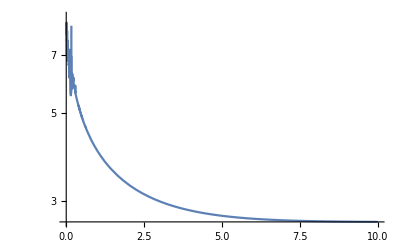

```mathematica
LogPlot[{err[t]},{t,0,10},PlotRange->All]
```

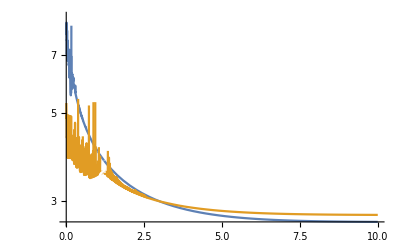

```mathematica
LogPlot[{err[t],err2[t]},{t,0,10},PlotRange->All]
```

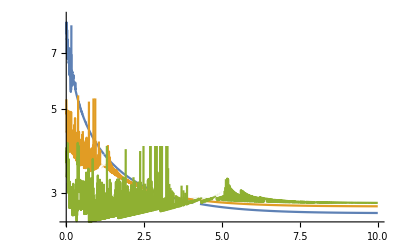

```mathematica
LogPlot[{err[t],err2[t],err3[t]},{t,0,10},PlotRange->All]
```

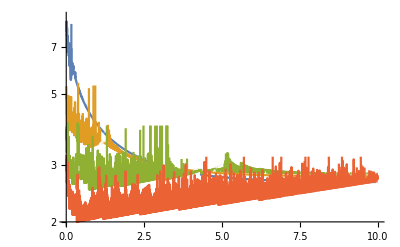

```mathematica
LogPlot[{err[t],err2[t],err3[t],err4[t]},{t,0,10},PlotRange->All]
```

#### Solving the equation exactly

```mathematica
eqn
```

1+u[t]-ϵ u[t]^2+u'[t]

```mathematica
u/.First@DSolve[{eqn==0},u,t]//Simplify
```

Function[{t},(1+√(-1-4 ϵ) Tan[1/2 (t √(-1-4 ϵ)+√(-1-4 ϵ) C[1])])/(2 ϵ)]

```mathematica
Integrate[1/(k(1+y^2)),y]
```

ArcTan[y]/k

This is no a good starting point because it becomes imaginary when ϵ = 0. Mathematica tries to match 1+u[t]-ϵ u[t]^2 to K(1 + y^2). Instead we need to get this to the form  K(1 - y^2).

```mathematica
(1+u-ϵ u^2) -c(1-(a+b u)^2)//Collect[#,u]&
```

1-c+a^2 c+(1+2 a b c) u+u^2 (b^2 c-ϵ)

```mathematica
const=Solve[{1-c+a^2 c==0,(1+2 a b c)==0,(b^2 c-ϵ)==0},{a,b,c}]
```

{{a→-1/(√(1+4 ϵ)),b→(2 ϵ)/(√(1+4 ϵ)),c→(1+4 ϵ)/(4 ϵ)},{a→1/(√(1+4 ϵ)),b→-(2 ϵ)/(√(1+4 ϵ)),c→(1+4 ϵ)/(4 ϵ)}}

```mathematica
Integrate[1/(c(1-(a+b y)^2)),y]//Together
```

(-Log[1-a-b y]+Log[1+a+b y])/(2 b c)

```mathematica
D[(-Log[1-a-b y]+Log[1+a+b y])/(2 b c),y]//Simplify
```

-1/(c (-1+a+b y) (1+a+b y))

```mathematica
Solve[(1+a+b u)/(1-a-b u) ==(1+a)/(1-a)Exp[-2b c t],u]
```

{{u→-((-1+a^2) (-1+ⅇ^(2 b c t)))/(b (-1-a-ⅇ^(2 b c t)+a ⅇ^(2 b c t)))}}

```mathematica
uExact1=-((-1+a^2) (-1+ⅇ^(2 b c t)))/(b (-1-a-ⅇ^(2 b c t)+a ⅇ^(2 b c t)))/.const[[1]]//Simplify
```

(2-2 ⅇ^(t √(1+4 ϵ)))/(-1+√(1+4 ϵ)+ⅇ^(t √(1+4 ϵ)) (1+√(1+4 ϵ)))

```mathematica
uExact2=-((-1+a^2) (-1+ⅇ^(2 b c t)))/(b (-1-a-ⅇ^(2 b c t)+a ⅇ^(2 b c t)))/.const[[2]]//Simplify
```

(2-2 ⅇ^(t √(1+4 ϵ)))/(-1+√(1+4 ϵ)+ⅇ^(t √(1+4 ϵ)) (1+√(1+4 ϵ)))

```mathematica
Series[uExact1,{ϵ,0,2}]
```

(-1+ⅇ^-t)+(1-ⅇ^(-2 t)-2 ⅇ^-t t) ϵ+(-2+ⅇ^(-3 t)+2 ⅇ^(-2 t)-ⅇ^-t+4 ⅇ^(-2 t) t+2 ⅇ^-t t+2 ⅇ^-t t^2) ϵ^2+O[ϵ]^3

```mathematica
Series[uExact2,{ϵ,0,2}]
```

(-1+ⅇ^-t)+(1-ⅇ^(-2 t)-2 ⅇ^-t t) ϵ+(-2+ⅇ^(-3 t)+2 ⅇ^(-2 t)-ⅇ^-t+4 ⅇ^(-2 t) t+2 ⅇ^-t t+2 ⅇ^-t t^2) ϵ^2+O[ϵ]^3

```mathematica
approx[ϵ]
```

-1+ⅇ^-t+(1-ⅇ^(-2 t)-2 ⅇ^-t t) ϵ+(-2+ⅇ^(-3 t)+2 ⅇ^(-2 t)-ⅇ^-t+4 ⅇ^(-2 t) t+2 ⅇ^-t t+2 ⅇ^-t t^2) ϵ^2

```mathematica
Series[uExact1,{ϵ,0,2}]-approx[ϵ]
```

O[ϵ]^3

```mathematica
Series[uExact2,{ϵ,0,2}]-approx[ϵ]
```

O[ϵ]^3

```mathematica
eqn
```

1+u[t]-ϵ u[t]^2+u'[t]

```mathematica
eqn/.u-> Function[{t},uExact1]//Simplify
```

(4 ⅇ^(t √(1+4 ϵ)) (1+4 ϵ))/((-1+√(1+4 ϵ)+ⅇ^(t √(1+4 ϵ)) (1+√(1+4 ϵ)))^2)

```mathematica
eqn/.u-> Function[{t},uExact2]//Simplify
```

(4 ⅇ^(t √(1+4 ϵ)) (1+4 ϵ))/((-1+√(1+4 ϵ)+ⅇ^(t √(1+4 ϵ)) (1+√(1+4 ϵ)))^2)